```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g=Flatten[Import["NoOffset/C/best.gen.dat"]];
```

```mathematica
sw = Import["NoOffset/C/sensorweights.dat"];
```

```mathematica
iw = Import["NoOffset/C/interweights.dat"];
```

```mathematica
mw = Import["NoOffset/C/motorweights.dat"];
```

```mathematica
ArrayPlot[sw,ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->250]
Export["sw.eps",%]
```

-Graphics-

sw.eps

```mathematica
ArrayPlot[iw,ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->250]
Export["iw.eps",%]
```

-Graphics-

iw.eps

```mathematica
ArrayPlot[Transpose[mw],ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->250]
Export["mw.eps",%]
```

-Graphics-

mw.eps

```mathematica
radius = 4;
```

```mathematica
anglelist=Table[(2 Pi / 5)x,{x,1,5}]
```

{(2 π)/5,(4 π)/5,(6 π)/5,(8 π)/5,2 π}

```mathematica
neuronpos =Table[{radius Sin[anglelist[[x]]],radius Cos[anglelist[[x]]]},{x,1,5}]
```

{{4 √(5/8+(√5)/8),-1+√5},{4 √(5/8-(√5)/8),-1-√5},{-4 √(5/8-(√5)/8),-1-√5},{-4 √(5/8+(√5)/8),-1+√5},{0,4}}

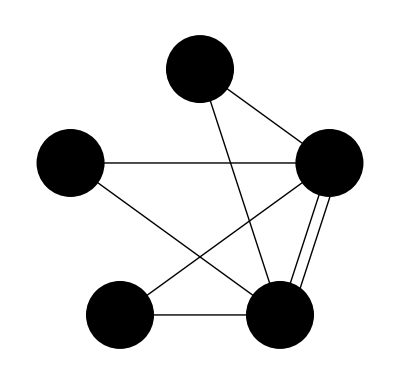

```mathematica
Graphics[
{
Disk[neuronpos[[1]]],
Disk[neuronpos[[2]]],
Disk[neuronpos[[3]]],
Disk[neuronpos[[4]]],
Disk[neuronpos[[5]]],
Line[{neuronpos[[1]]+0.5,neuronpos[[2]]+0.5}],
Line[{neuronpos[[1]],neuronpos[[3]]}],
Line[{neuronpos[[1]],neuronpos[[4]]}],
Line[{neuronpos[[1]],neuronpos[[5]]}],
Line[{neuronpos[[2]],neuronpos[[1]]}],
Line[{neuronpos[[2]],neuronpos[[3]]}],
Line[{neuronpos[[2]],neuronpos[[4]]}],
Line[{neuronpos[[2]],neuronpos[[5]]}]
}
]
```